```mathematica
ass={r>0,z'[r]^2>0,CC>0}
```

{r>0,z'[r]^2>0,CC>0}

```mathematica
(*canoincal base vectors*)
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
g[r_]:={{1+(z'[r])^2,0},{0,r^2}}
```

```mathematica
detg[r_]:=Det[g[r]]
```

```mathematica
sqrtdetg[r_]:=Sqrt[detg[r]]
```

```mathematica
ig[r_]:=Inverse[g[r]]//FullSimplify
```

```mathematica
ig[r]
```

{{1/(1+z'[r]^2),0},{0,1/r^2}}

```mathematica
e[1][x_]:={Cos[x[[2]]], Sin[x[[2]]],z'[x[[1]]]} 
e[2][x_]:= {-x[[1]]Sin[x[[2]]],x[[1]] Cos[x[[2]]],0}
```

```mathematica
normal[x_]:=FullSimplify[Cross[e[1][x],e[2][x]]/sqrtdetg[x[[1]]],Assumptions->ass]
```

```mathematica
N3d[x_]:={-Cos[x[[2]]],-Sin[x[[2]]],0}
```

```mathematica
Clear[normNt]
```

```mathematica
Nt[r_]:=FullSimplify[Table[Sum[ig[r][[i,j]](N3d[{r,θ}].e[j][{r,θ}]),{j,1,2}],{i,1,2}],Assumptions->ass]
```

```mathematica
(*norm of Nt with respect to g*)
```

```mathematica
normNt[r_]:= Sqrt[Sum[Nt[r][[i]] Nt[r][[j]]*g[r][[i,j]],{i,1,2},{j,1,2}]]
```

```mathematica
Nt[r]/normNt[r]
```

{-√(1/(1+z'[r]^2)),0}

```mathematica
(*n^i at \partial \Omega_r*)
```

```mathematica
nRmin[x_]:=FullSimplify[{-x[[1]]/sqrtdetg[x[[1]]],0},Assumptions->ass]
```

```mathematica
(*n^i at \partial \Omega_R*)
```

```mathematica
nRmax[x_]:=FullSimplify[{x[[1]]/sqrtdetg[x[[1]]],0},Assumptions->ass]
```

```mathematica
(*omegaRmin(max)_here = omega_r(R)_const{variational_problem_bc_ring.py}*)
```

```mathematica
omegaRmin=nRmin[{Rmin,θ}].{z'[Rmin],0}
```

-(Rmin z'[Rmin])/(√(Rmin^2 (1+z'[Rmin]^2)))

```mathematica
omegaRmax=nRmax[{Rmax,θ}].{z'[Rmax],0}
```

(Rmax z'[Rmax])/(√(Rmax^2 (1+z'[Rmax]^2)))

```mathematica
(*second fundamental form b*)
```

```mathematica
Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}]//FullSimplify
```

z''[r]/(√(1+z'[r]^2))

```mathematica
Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}]//FullSimplify
```

0

```mathematica
Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}]//FullSimplify
```

0

```mathematica
Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]//FullSimplify
```

(r z'[r])/(√(1+z'[r]^2))

```mathematica
b[r_]:={{Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}]},{Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]}}//FullSimplify
```

```mathematica
H[r_]:=1/2 Tr[ig[r].b[r]]//FullSimplify
```

```mathematica
K[r_]:=Det[b[r]]/detg[r]//FullSimplify
```

```mathematica
(*this is the function which appears under derivative in - \Nabla_{LB} H*)
```

```mathematica
ϕ[r_]:=(r^2 H'[r])/sqrtdetg[r]
```

```mathematica
FullSimplify[ϕ'[r],Assumptions->ass]
```

```mathematica
eq=FullSimplify[{κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ [r]H[r]==0},Assumptions->ass]
```

```mathematica
(*
z[r_]:=CC * r
FullSimplify[κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ [r]H[r],Assumptions->ass]
FullSimplify[Solve[(CC (-((2+CC^2) κ)+2 (1+CC^2) r^2 σ[r]))/(2 (1+CC^2)^(3/2) r^3)==0,σ[r]][[1]],Assumptions->ass]
*)
```

```mathematica
(*z[r_]:=CC * r^2
FullSimplify[κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ [r]H[r],Assumptions->ass]
FullSimplify[Solve[FullSimplify[κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ [r]H[r],Assumptions->ass]==0,σ[r]][[1]],Assumptions->ass]*)
```

```mathematica
κ=1;
CC=1/10;
Rmin=1;
Rmax=2;
z[r_]:=CC * Cos[2 π r]
FullSimplify[Solve[FullSimplify[κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ [r]H[r],Assumptions->ass]==0,σ[r]][[1]],Assumptions->ass]
```

{σ[r]→(-1000 π r (-400000+π^2 (-6000+π^4+320 (-5000+25 π^2+24 π^4) r^2)) Cos[2 π r]+600 π^3 r (-10000+3 π^4+11200 π^2 (25+π^2) r^2) Cos[6 π r]+1000 π^7 r (-1+960 r^2) Cos[10 π r]+200 π^7 r Cos[14 π r]-2 (100000000+π^2 (10500000+450000 π^2+8750 π^4+63 π^6-200000 (4000+390 π^2+7 π^4) r^2)) Sin[2 π r]+4 π^2 (1750000+21 π^6+125 π^4 (21-400 r^2)+12500 π^2 (9+560 r^2)) Sin[6 π r]-4 π^4 (22500+9 π^4+125 π^2 (7+880 r^2)) Sin[10 π r]+π^6 (500+9 π^2) Sin[14 π r]-π^8 Sin[18 π r])/(64 r^2 (-50-π^2+π^2 Cos[4 π r])^3 (50 π r Cos[2 π r]+25 Sin[2 π r]+π^2 Sin[2 π r]^3))}

```mathematica
κ=1;
CC=1/10;
(*
z[r_]:=CC * r
σ[r_]:=((2+CC^2) κ)/(2 (1+CC^2) r^2)
Rmin=1;
Rmax=2;
zRmin=CC Rmin;
zRmax=CC Rmax;
zpRmin=CC;
zpRmax=CC;
*)
(*z[r_]:=CC * r^2*)
σ[r_]:=(16 CC^2 (-1+6 CC^2 r^2+6 CC^4 r^4+4 CC^6 r^6) κ)/((1+2 CC^2 r^2) (1+4 CC^2 r^2)^3)
Rmin=1;
Rmax=2;
zRmin=CC Rmin^2;
zRmax=CC Rmax^2;
zpRmin=2CC Rmin;
zpRmax=2 CC Rmax;
```

```mathematica
bcs={z[Rmin]==zRmin,z[Rmax]==zRmax,z'[Rmin]==zpRmin,z'[Rmax]==zpRmax};
```

```mathematica
s=NDSolve[Flatten[{eq,bcs}],z,{r,Rmin,Rmax}]
```

{{z→InterpolatingFunction[…]}}

```mathematica
Clear[r]
```

```mathematica
err=Table[{r,(κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ[r]H[r])/.s[[1]]},{r,Rmin,Rmax,0.01}]
```

```mathematica
Max[Table[Abs[err[[i,2]]],{i,1,Length[err]}]]
```

0.0000383604

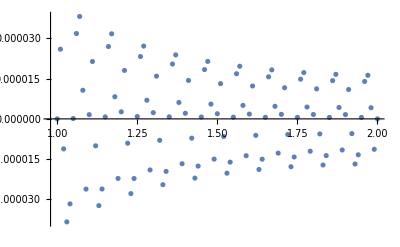

```mathematica
ListPlot[Table[{r,(κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ[r]H[r])/.s[[1]]},{r,Rmin,Rmax,0.01}],PlotRange->Full]
```

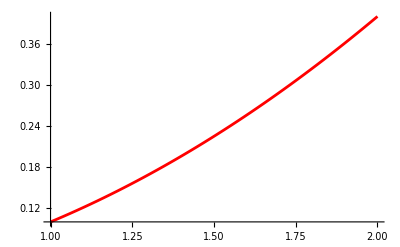

```mathematica
plotzex=Plot[Evaluate[z[r]/. s],{r,Rmin,Rmax},PlotRange->All, PlotStyle->Red]
```

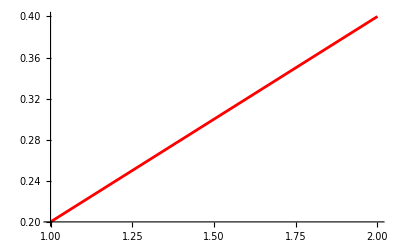

```mathematica
plotωex=Plot[Evaluate[z'[r]/. s],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Red]
```

```mathematica
(*check z*)
```

```mathematica
znum=Import["~/Documents/finite_elements/solution/z.csv"];
znum=Table[{Sqrt[znum[[i,2]]^2+znum[[i,3]]^2],znum[[i,1]]},{i,2,Length[znum]}]
```

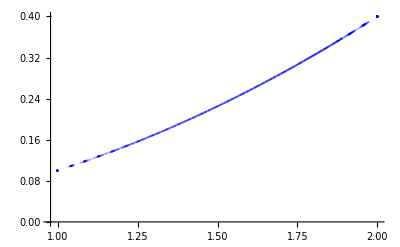

```mathematica
plotnum=ListPlot[znum,PlotRange->Full,PlotStyle->{Blue,Opacity->0.05}]
```

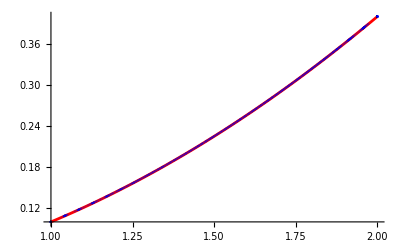

```mathematica
Show[plotzex,plotnum]
```

```mathematica
(*check ω*)
```

```mathematica
ω=Import["~/Documents/finite_elements/solution/omega.csv"];
ω=Table[{Sqrt[ω[[i,4]]^2+ω[[i,5]]^2],ω[[i,4]]/Sqrt[ω[[i,4]]^2+ω[[i,5]]^2] ω[[i,1]]+ω[[i,5]]/Sqrt[ω[[i,4]]^2+ω[[i,5]]^2] ω[[i,2]]},{i,2,Length[ω]}]
```

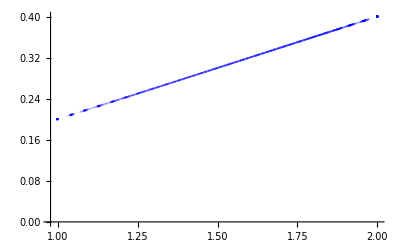

```mathematica
plotωnum=ListPlot[ω,PlotStyle->{Blue,Opacity->0.05}]
```

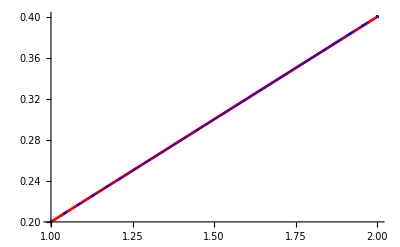

```mathematica
Show[plotωex,plotωnum]
```